```mathematica
2-2
```

0

```mathematica
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
```

# Quantum Motion of a Particle in a Box

Nicholas Wheeler
Reed College Physics Department
18 August 2008

### Introduction

It is by way of preparation for discussion of "quantum Liossajous figures" and "quantum vorticity" that I look here to aspects—specifically, dynamics aspects—of the simplest and most familiar of all quantum mechanical systems: the "particle-in-a-box" problem. I work first in one dimension, then by straightforward generalization in two dimensions.

Two-dimensional theory

We redirect our attention now to properties of the solutions of

-ℏ^2/(2m)(∂_(x,x) +∂_(y,y))ψ[x,y,t]=ⅈ ℏ ∂_t ψ[x,y,t]

that conform to the boundary conditions

ψ[0,0,t]=ψ[a,0,t]=ψ[0,a,t]=ψ[a,a,t]=0    :    all  t

If we adopt units in which

ℏ=2m=a=1

we have

-(∂_(x,x) +∂_(y,y))ψ[x,t]=ⅈ  ∂_t ψ[x,t]
ψ[0,t]=ψ[1,t]    :    all  t

which is easier to work with. If we assume the wave function to have separated structure

ψ[x,y,t]=Ψ_1[x]*Ψ_2[y]*ⅇ^(-ⅈ ω t)

and are led immediately to the orthonormal eigenfunctions

```mathematica
Ψ[x_,y_,m_,n_]:=2 Sin[m π x]Sin[n π y]
```

```mathematica
Plot3D[Ψ[x,y,2,3],{x,0,1},{y,0,1},LabelStyle->Directive[Bold], PlotLabel->"The {2, 3} Eigenstate" ]
Plot3D[Ψ[x,y,2,3]^2,{x,0,1},{y,0,1},LabelStyle->Directive[Bold], PlotLabel->"The {2, 3} Probability Distribution"]
```

-Graphics3D-

-Graphics3D-

From

```mathematica
-D[Ψ[x,y,m,n], x,x]-D[Ψ[x,y,m,n], y,y]==(m^2+n^2) π^2 Ψ[x,y,m,n]//Simplify
```

True

we are led to define the "eigenfrequencies"

```mathematica
ω[m_,n_]:=(m^2+n^2)π^2
```

and to construct the "buzz factors"

```mathematica
Clear[BuzzFactor]
```

```mathematica
BuzzFactor[m_,n_,t_]:=ⅇ^(-ⅈ ω[m,n] t)
```

The time-dependent eigenfunctions are given now by

```mathematica
ψ[x_,y_,m_,n_,t_]:=Ψ[x,y,m,n]*BuzzFactor[m,n,t]
```

which we verify do satisfy the time-dependent Schrøodinger equation:

```mathematica
-D[ψ[x,y,m,n,t], x,x]-D[ψ[x,y,m,n,t], y,y]==ⅈ D[ψ[x,y,m,n,t], t]//Simplify
```

True

The function ψ[x, y, m, n, t], since complex-valued, does not lend itself to graphic representation (people sometimes graph the amplitude, and use color to indicate the t-dependent phase), and there is no reason to graph the "moving probability amplitude," since it does not move! To see motion one must look to weighted linear combinations of eigenfunctions that buzz with distinct frequencies.

Motion of simple 2D superpositions

One must be careful to distinguish superpositions of the form

```mathematica
ϕ[x,y,t]=(∑_m Subscript[A, m] ψ[x,m,t])*(∑_n Subscript[B, n] ψ[x,n,t])
```

— which are assembled from products of sums of one-dimensional buzzing eigenfunctions

```mathematica
Ψ[x_,n_]:=√2 Sin[n π x]
ψ[x_,n_,t_]:=Ψ[x,n]*ⅇ^(-ⅈ n^2 π^2 t)
```

—from superpositions of the form

```mathematica
Φ[x,y,t]=∑_m ∑_n Subscript[C, mn] ψ[x,y,m,n,t]
```

which are sums of products of one-dimensional buzzing eigenfunctions. The former give rise in the classical limit to Lissajous figures, and the latter to more complex kinds of quantum motion. I look to the alternatives in the order stated.

First approach to the quantum theory of Lissajous figures

The classical motion of a partticle that moves freely within a one-dimensional bounding box is shown in the figure which I now construct:

```mathematica
A=Table[{{2n-x0-v t,((2n-1)-x0)/v<t<(2n-x0)/v},
{v t-2n+x0,(2n-x0)/v<t<((2n+1)-x0)/v}},{n,0,50}];
```

```mathematica
Segments={Part[A,1,1],Part[A,1,2],Part[A,2,1],Part[A,2,2],
Part[A,3,1],Part[A,3,2],Part[A,4,1],Part[A,4,2],
Part[A,5,1],Part[A,5,2],Part[A,6,1],Part[A,6,2],
Part[A,7,1],Part[A,7,2],Part[A,8,1],Part[A,8,2],
Part[A,9,1],Part[A,9,2],Part[A,10,1],Part[A,10,2],
Part[A,11,1],Part[A,11,2],Part[A,12,1],Part[A,12,2],
Part[A,13,1],Part[A,13,2],Part[A,14,1],Part[A,14,2],
Part[A,15,1],Part[A,15,2],Part[A,16,1],Part[A,16,2],
Part[A,17,1],Part[A,17,2],Part[A,18,1],Part[A,18,2],
Part[A,19,1],Part[A,19,2],Part[A,20,1],Part[A,20,2],
Part[A,21,1],Part[A,21,2],Part[A,22,1],Part[A,22,2],
Part[A,23,1],Part[A,23,2],Part[A,24,1],Part[A,24,2],
Part[A,25,1],Part[A,25,2],Part[A,26,1],Part[A,26,2],
Part[A,27,1],Part[A,27,2],Part[A,28,1],Part[A,28,2],
Part[A,29,1],Part[A,29,2],Part[A,30,1],Part[A,30,2],
Part[A,31,1],Part[A,31,2],Part[A,32,1],Part[A,32,2],
Part[A,33,1],Part[A,33,2],Part[A,34,1],Part[A,34,2],
Part[A,35,1],Part[A,35,2],Part[A,36,1],Part[A,36,2],
Part[A,37,1],Part[A,37,2],Part[A,38,1],Part[A,38,2],Part[A,39,1],Part[A,39,2],Part[A,40,1],Part[A,40,2],
Part[A,41,1],Part[A,41,2],Part[A,42,1],Part[A,42,2],
Part[A,43,1],Part[A,43,2],Part[A,44,1],Part[A,44,2],
Part[A,45,1],Part[A,45,2],Part[A,46,1],Part[A,46,2],Part[A,47,1],Part[A,47,2],Part[A,48,1],Part[A,48,2],
Part[A,49,1],Part[A,49,2],Part[A,50,1],Part[A,50,2]};
```

```mathematica
x[t_]:=Piecewise[Segments]
```

That function serves to describe the motion of such a particle for times

0<t<(99-x0)/v

Assigning particular values to the speed and initial position

```mathematica
X[t_]:=x[t]/.{x0->0.4, v->1}
```

we obtain the figure

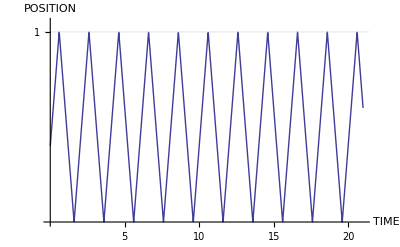

```mathematica
Plot[Evaluate[X[t]],{t,0,21},PlotRange->{0,1.05}, GridLines->{{},{1}}, Ticks->{{5,10,15,20},{1}}, AxesLabel->{"TIME","POSITION"}]
```

A description of the motion of a free particle trapped within a 2-dimensional box is obtained by forming the tensor product of the preceding construction:

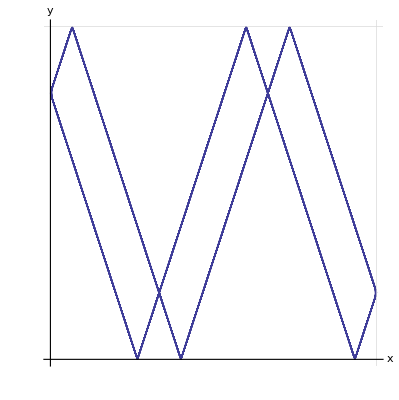

```mathematica
X[t_] := x[t] /. {x0 -> .4, v -> 1}
Y[t_] := x[t] /. {x0 -> 0, v -> 3}
ParametricPlot[Evaluate[{X[t],Y[t]}], {t,0,20},GridLines->{{1},{1}}, Ticks->False, AxesLabel->{x,y}, LabelStyle->Large]
```

Here is a slightly de-tuned variant of the preceding figure:

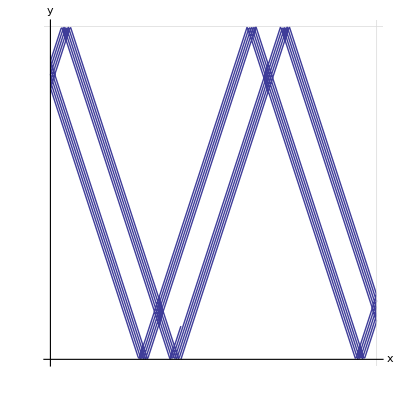

```mathematica
X[t_] := x[t] /. {x0 -> .4, v -> 1}
Y[t_] := x[t] /. {x0 -> 0, v -> 3.01}
ParametricPlot[Evaluate[{X[t],Y[t]}], {t,0,10},GridLines->{{1},{1}}, Ticks->False, AxesLabel->{x,y}, LabelStyle->Large]
```

The following commands permit one to construct unlimitedly many slightly de-tuned instances of the simplest kind of Lissajous figures—those in which right/left and up/down traversals occur with the same (or nearly the same) period:

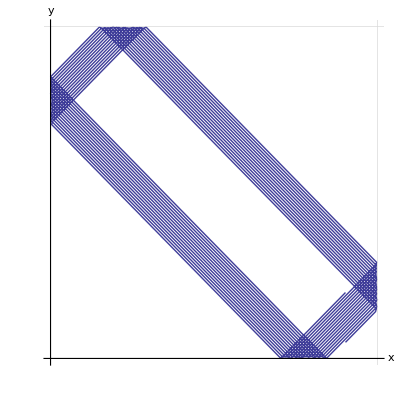

```mathematica
X[t_] := x[t] /. {x0 ->RandomReal[], v ->1}
Y[t_] := x[t] /. {x0 ->RandomReal[], v ->1.005}
ParametricPlot[Evaluate[{X[t],Y[t]}], {t,0,30},GridLines->{{1},{1}}, Ticks->False, AxesLabel->{x,y}, LabelStyle->Large]
```

I turn now to the construction of a quantum state that executes a "soft" Lissajous figure. It proceeds from the assumption that x and y are independent random variables. From

```mathematica
Clear[x]
```

```mathematica
ϕx[x_,t_,α_]:=Cos[α] √2 Sin[π 1 x] ⅇ^(-ⅈ 1^2 t)+Sin[α] √2 Sin[π 2 x] ⅇ^(-ⅈ 2^2 t)
ϕy[y_,t_,β_]:=Cos[β] √2 Sin[π 3 y] ⅇ^(-ⅈ 3^2 t)+Sin[β] √2 Sin[π 4 y] ⅇ^(-ⅈ 4^2 t)
```

(where α and β are "mixing angles") construct

We construct the probability density associated with ϕx[x, t, α] and

```mathematica
Px[x_,t_,α_]:=(ComplexExpand[Re[ϕx[x,t,α]]])^2+(ComplexExpand[Im[ϕx[x,t,α]]])^2
```

```mathematica
TrigReduce[Px[x,t,α]]
```

1/4 (4-2 Cos[2 π x]-2 Cos[4 π x]-Cos[2 π x-2 α]+Cos[4 π x-2 α]-Cos[2 π x+2 α]+Cos[4 π x+2 α]+Sin[3 t-3 π x-2 α]-Sin[3 t-π x-2 α]-Sin[3 t+π x-2 α]+Sin[3 t+3 π x-2 α]-Sin[3 t-3 π x+2 α]+Sin[3 t-π x+2 α]+Sin[3 t+π x+2 α]-Sin[3 t+3 π x+2 α])

and see that it has angular frequency

```mathematica
Subscript[Ω, x]=3
```

Experimentation leads us to set α  = 0.64 (in order to get a good clear slosh); the moving distribution looks like this:

```mathematica
Animate[Plot[Px[x,t,0.64],{x,0,1}, PlotRange->{0,3}],{t,0,(2π)/3}]
```

Similarly,

```mathematica
Py[y_,t_,β_]:=(ComplexExpand[Re[ϕy[y,t,β]]])^2+(ComplexExpand[Im[ϕy[y,t,β]]])^2
```

```mathematica
TrigReduce[Py[x,t,β]]
```

1/4 (4-2 Cos[6 π x]-2 Cos[8 π x]-Cos[6 π x-2 β]+Cos[8 π x-2 β]-Cos[6 π x+2 β]+Cos[8 π x+2 β]+Sin[7 t-7 π x-2 β]-Sin[7 t-π x-2 β]-Sin[7 t+π x-2 β]+Sin[7 t+7 π x-2 β]-Sin[7 t-7 π x+2 β]+Sin[7 t-π x+2 β]+Sin[7 t+π x+2 β]-Sin[7 t+7 π x+2 β])

is seen to have angular frequency

```mathematica
Subscript[Ω, y]=7
```

Experimentation leads us to set β = 3.77, producing a sloshing distribution that looks like this:

```mathematica
Animate[Plot[Py[y,t,3.77],{y,0,1}, PlotRange->{0,4}],{t,0,(2π)/7}]
```

We assume the composite wavefunction to have the factored structure

```mathematica
Φ[x_,y_,t_]:=ϕx[x,t,0.64]*ϕy[y,t,3.77]
```

```mathematica
Φ[x,y,t]
```

(1.13433 ⅇ^(-ⅈ t) Sin[π x]+0.844562 ⅇ^(-4 ⅈ t) Sin[2 π x]) (-1.14405 ⅇ^(-9 ⅈ t) Sin[3 π y]-0.831355 ⅇ^(-16 ⅈ t) Sin[4 π y])

which is, in effect, to assume that x and y are independent random variables.

We assemble the associated probability density

```mathematica
P[x_,y_,t_]:=(ComplexExpand[Re[Φ[x,y,t]]])^2+(ComplexExpand[Im[Φ[x,y,t]]])^2
```

This is seen to be quite a complicated expression

```mathematica
TrigReduce[P[x,y,t]]//Chop
```

1.-0.643358 Cos[2 π x]-0.356642 Cos[4 π x]-0.479008 Cos[3 t-3 π x]+0.479008 Cos[3 t-π x]+0.479008 Cos[3 t+π x]-0.479008 Cos[3 t+3 π x]-0.654424 Cos[6 π y]-0.345576 Cos[8 π y]+0.0827668 Cos[3 t-3 π x-8 π y]-0.0827668 Cos[3 t-π x-8 π y]-0.0827668 Cos[3 t+π x-8 π y]+0.111164 Cos[2 π x-8 π y]+0.0827668 Cos[3 t+3 π x-8 π y]+0.0616235 Cos[4 π x-8 π y]-0.475556 Cos[7 t-7 π y]+0.0848017 Cos[7 t-4 π x-7 π y]+0.113897 Cos[4 t-3 π x-7 π y]+0.113897 Cos[10 t-3 π x-7 π y]+0.152976 Cos[7 t-2 π x-7 π y]-0.113897 Cos[4 t-π x-7 π y]-0.113897 Cos[10 t-π x-7 π y]-0.113897 Cos[4 t+π x-7 π y]-0.113897 Cos[10 t+π x-7 π y]+0.152976 Cos[7 t+2 π x-7 π y]+0.113897 Cos[4 t+3 π x-7 π y]+0.113897 Cos[10 t+3 π x-7 π y]+0.0848017 Cos[7 t+4 π x-7 π y]+0.156737 Cos[3 t-3 π x-6 π y]-0.156737 Cos[3 t-π x-6 π y]-0.156737 Cos[3 t+π x-6 π y]+0.210514 Cos[2 π x-6 π y]+0.156737 Cos[3 t+3 π x-6 π y]+0.116698 Cos[4 π x-6 π y]+0.475556 Cos[7 t-π y]-0.0848017 Cos[7 t-4 π x-π y]-0.113897 Cos[4 t-3 π x-π y]-0.113897 Cos[10 t-3 π x-π y]-0.152976 Cos[7 t-2 π x-π y]+0.113897 Cos[4 t-π x-π y]+0.113897 Cos[10 t-π x-π y]+0.113897 Cos[4 t+π x-π y]+0.113897 Cos[10 t+π x-π y]-0.152976 Cos[7 t+2 π x-π y]-0.113897 Cos[4 t+3 π x-π y]-0.113897 Cos[10 t+3 π x-π y]-0.0848017 Cos[7 t+4 π x-π y]+0.475556 Cos[7 t+π y]-0.0848017 Cos[7 t-4 π x+π y]-0.113897 Cos[4 t-3 π x+π y]-0.113897 Cos[10 t-3 π x+π y]-0.152976 Cos[7 t-2 π x+π y]+0.113897 Cos[4 t-π x+π y]+0.113897 Cos[10 t-π x+π y]+0.113897 Cos[4 t+π x+π y]+0.113897 Cos[10 t+π x+π y]-0.152976 Cos[7 t+2 π x+π y]-0.113897 Cos[4 t+3 π x+π y]-0.113897 Cos[10 t+3 π x+π y]-0.0848017 Cos[7 t+4 π x+π y]+0.156737 Cos[3 t-3 π x+6 π y]-0.156737 Cos[3 t-π x+6 π y]-0.156737 Cos[3 t+π x+6 π y]+0.210514 Cos[2 π x+6 π y]+0.156737 Cos[3 t+3 π x+6 π y]+0.116698 Cos[4 π x+6 π y]-0.475556 Cos[7 t+7 π y]+0.0848017 Cos[7 t-4 π x+7 π y]+0.113897 Cos[4 t-3 π x+7 π y]+0.113897 Cos[10 t-3 π x+7 π y]+0.152976 Cos[7 t-2 π x+7 π y]-0.113897 Cos[4 t-π x+7 π y]-0.113897 Cos[10 t-π x+7 π y]-0.113897 Cos[4 t+π x+7 π y]-0.113897 Cos[10 t+π x+7 π y]+0.152976 Cos[7 t+2 π x+7 π y]+0.113897 Cos[4 t+3 π x+7 π y]+0.113897 Cos[10 t+3 π x+7 π y]+0.0848017 Cos[7 t+4 π x+7 π y]+0.0827668 Cos[3 t-3 π x+8 π y]-0.0827668 Cos[3 t-π x+8 π y]-0.0827668 Cos[3 t+π x+8 π y]+0.111164 Cos[2 π x+8 π y]+0.0827668 Cos[3 t+3 π x+8 π y]+0.0616235 Cos[4 π x+8 π y]

```mathematica
Length[%]
```

85

in which the time variable enters (via cross terms—interference terms) with the following factors:

```mathematica
{3, 4, 7, 10}
```

of which the least common multiple is

```mathematica
LCM[3,4,7,10]
```

420

But  P[x, y, t]  is actually not so complicated as it seems. It is the product of two simple slosh functions that have already been shown to have angular frequencies 3 and 7, respectively:

```mathematica
PXTPYT=Expand[Px[x,t,0.64]*Py[y,t,3.77]];
PXYT=Expand[P[x,y,t]];

PXYT-PXTPYT//Chop
```

0

The 4 and 10 arise as artifacts of the multiplication process:

```mathematica
{3,7-3 ,7,7+3 }
```

{3,4,7,10}

The following figures give some indication of the initial motion of the bi-variate probability distribution:

```mathematica
Table[Plot3D[Evaluate[P[x,y,n/5 ]],{x,0,1},{y,0,1}, PlotRange->{0,12},Ticks->False],{n,0,25}]//TableForm
```

-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-

The motion appears to be "Lissajous-like" only in some very soft sense. But the situation gains sharpness when one looks to the  motion of the expected position of the quantum particle:

```mathematica
ExpPositionData=Table[NIntegrate[{x,y}P[x,y,n/20],{x,0,1},{y,0,1}],{n,0,100}];
```

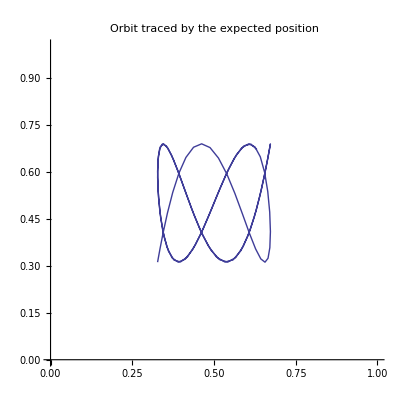

```mathematica
QuantumOrbit=ListPlot[ExpPositionData,Joined->True, PlotRange->{{0,1}, {0,1}},PlotLabel->"Orbit traced by the expected position", AspectRatio->Automatic]
```

An excellent approxiation to such a figure—viewed simply as a mathematical object—could be produced by much simpler means:

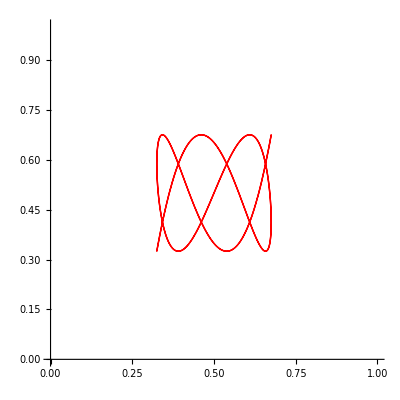

```mathematica
ApproximatingSimpleLissajous=ParametricPlot[{.5+.175Sin[(2π)/7 t],.5+.175Sin[(2π)/3 t]}, {t,0,21},PlotRange->{{0,1}, {0,1}}, PlotStyle->Red]
```

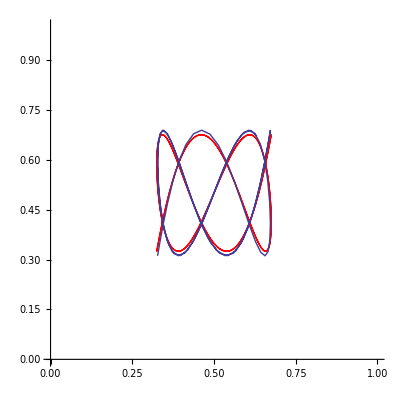

```mathematica
Show[ApproximatingSimpleLissajous,QuantumOrbit]
```

```mathematica
X[t_] := x[t] /. {x0 -> 0, v ->1}
Y[t_] := x[t] /. {x0 -> 0, v -> 7/3}
ParametricPlot[Evaluate[{X[t],Y[t]}], {t,0,20},GridLines->{{1},{1}}, Ticks->False, AxesLabel->{x,y}, LabelStyle->Large]
```

Of course, the trajectories traced by a classical particle confined to the interior of a square box are assembled from straight segments. In cases with

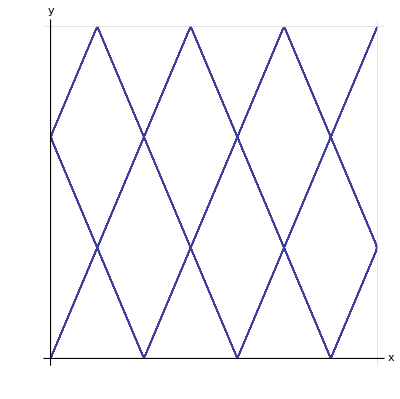

```mathematica
Subscript[v, x]/Subscript[v, y]=3/7
```

We expect the moving quantum expectation value of position to trace an improved approximation to such a curve (with less rounded corners than were obtained previously) if we construct

Px[x,t]
Py[y,t]

by launching wavepackets that are intially well localized, and keep t so short that the localization remains well-preserved. The computational burden of such an approach is, however, great, so I will not attempt to illustrate the remark by explicit example. In such "hard" situations the moving function P[x, y, t] would itself—not just the associated expectation values, and except for complications at the reflection points—trace (for a while) a recognizable approximation to a Lissajous figure.

An alternative approach to the  quantum theory of Lissajous figures

Recently, Y. F. Chen, K, F, Huang & Y. P. Lan were led ("Localization of wave patterns on classical periodic orbits in a square billiard," Phys. Rev. E 66, 046215 (2002); "Quantum manifestations of classical periodic orbits in a square billiard: Formation of vortex lattices,"  Phys. Rev. E 66, 066210 (2002))—by appropriating the "Schwinger representation of the SU(2) algebra," a train of thought which I will not attempt to reproduce—to write (in my notation)

```mathematica
Clear[Ψ]
```

```mathematica
Ψ[x_,y_,m_,n_]:=2 Sin[m π x]Sin[n π y]
```

```mathematica
Ψ[x,y,k+1,n-k+1]
```

2 Sin[(1+k) π x] Sin[(1-k+n) π y]

and from those functions to construct

```mathematica
Chen[x_,y_,n_, p_, q_,ϕ_]:=1/2^(n/2)∑_(k=0)^n √Binomial[n,k] ⅇ^(ⅈ k ϕ)Ψ[p x,q y,k+1,n-k+1]
```

```mathematica
Chen[x,y,10, 7,3,0]
```

1/32 (2 Sin[77 π x] Sin[3 π y]+2 √10 Sin[70 π x] Sin[6 π y]+6 √5 Sin[63 π x] Sin[9 π y]+4 √30 Sin[56 π x] Sin[12 π y]+2 √210 Sin[49 π x] Sin[15 π y]+12 √7 Sin[42 π x] Sin[18 π y]+2 √210 Sin[35 π x] Sin[21 π y]+4 √30 Sin[28 π x] Sin[24 π y]+6 √5 Sin[21 π x] Sin[27 π y]+2 √10 Sin[14 π x] Sin[30 π y]+2 Sin[7 π x] Sin[33 π y])

```mathematica
DensityPlot[Chen[x,y,10, 7,3,0]^2,{x,0,1},{y,0,1}, PlotPoints->100]
```

-Graphics-

```mathematica
Chen[x,y,26, 7,3,0]
```

1/8192(2 Sin[189 π x] Sin[3 π y]+2 √26 Sin[182 π x] Sin[6 π y]+10 √13 Sin[175 π x] Sin[9 π y]+20 √26 Sin[168 π x] Sin[12 π y]+10 √598 Sin[161 π x] Sin[15 π y]+4 √16445 Sin[154 π x] Sin[18 π y]+2 √230230 Sin[147 π x] Sin[21 π y]+20 √6578 Sin[140 π x] Sin[24 π y]+10 √62491 Sin[133 π x] Sin[27 π y]+10 √124982 Sin[126 π x] Sin[30 π y]+2 √5311735 Sin[119 π x] Sin[33 π y]+8 √482885 Sin[112 π x] Sin[36 π y]+20 √96577 Sin[105 π x] Sin[39 π y]+20 √104006 Sin[98 π x] Sin[42 π y]+20 √96577 Sin[91 π x] Sin[45 π y]+8 √482885 Sin[84 π x] Sin[48 π y]+2 √5311735 Sin[77 π x] Sin[51 π y]+10 √124982 Sin[70 π x] Sin[54 π y]+10 √62491 Sin[63 π x] Sin[57 π y]+20 √6578 Sin[56 π x] Sin[60 π y]+2 √230230 Sin[49 π x] Sin[63 π y]+4 √16445 Sin[42 π x] Sin[66 π y]+10 √598 Sin[35 π x] Sin[69 π y]+20 √26 Sin[28 π x] Sin[72 π y]+10 √13 Sin[21 π x] Sin[75 π y]+2 √26 Sin[14 π x] Sin[78 π y]+2 Sin[7 π x] Sin[81 π y])

```mathematica
DensityPlot[Chen[x,y,26, 7,3,0]^2,{x,0,1},{y,0,1}, PlotPoints->100]
```

-Graphics-

### Vorticity

The preceding figure arises from deftly weighted superposition of a remarkably short list of eigenfunctions

```mathematica
Chen[x,y,26, 7,3,0]
```

1/8192(2 Sin[189 π x] Sin[3 π y]+2 √26 Sin[182 π x] Sin[6 π y]+10 √13 Sin[175 π x] Sin[9 π y]+20 √26 Sin[168 π x] Sin[12 π y]+10 √598 Sin[161 π x] Sin[15 π y]+4 √16445 Sin[154 π x] Sin[18 π y]+2 √230230 Sin[147 π x] Sin[21 π y]+20 √6578 Sin[140 π x] Sin[24 π y]+10 √62491 Sin[133 π x] Sin[27 π y]+10 √124982 Sin[126 π x] Sin[30 π y]+2 √5311735 Sin[119 π x] Sin[33 π y]+8 √482885 Sin[112 π x] Sin[36 π y]+20 √96577 Sin[105 π x] Sin[39 π y]+20 √104006 Sin[98 π x] Sin[42 π y]+20 √96577 Sin[91 π x] Sin[45 π y]+8 √482885 Sin[84 π x] Sin[48 π y]+2 √5311735 Sin[77 π x] Sin[51 π y]+10 √124982 Sin[70 π x] Sin[54 π y]+10 √62491 Sin[63 π x] Sin[57 π y]+20 √6578 Sin[56 π x] Sin[60 π y]+2 √230230 Sin[49 π x] Sin[63 π y]+4 √16445 Sin[42 π x] Sin[66 π y]+10 √598 Sin[35 π x] Sin[69 π y]+20 √26 Sin[28 π x] Sin[72 π y]+10 √13 Sin[21 π x] Sin[75 π y]+2 √26 Sin[14 π x] Sin[78 π y]+2 Sin[7 π x] Sin[81 π y])

```mathematica
Length[Expand[Chen[x,y,26, 7,3,0]]]
```

27

The point to which I would draw attention is that the associated probability density now does not have the form

```mathematica
Px[x]*Py[y]
```

The x and y variables are now correlated—not statistically independent.